Data. Columns: Vcc (actual), ADC0 (temp), ADC1 (voltage)

```mathematica
data=Import["~/src/xbee_temp_sensor/calibration/vinvout.csv"];TableForm[data]
```

2.562 | 4619 | 3416
2.8.32 | 4615 | 3769
3.013 | 4409 | 3957
3.234 | 4392 | 3840
3.506 | 4388 | 4280
4.04 | 4282 | 4800
4.23 | 4248 | 5136
4.49 | 4184 | 6144
4.74 | 4112 | 7488
5.01 | 4088 | 8064
5.24 | 4128 | 8112
5.52 | 6144 | 8172

Actual VREF (measured)

```mathematica
vref=1221;
```

Voltage divider coefficient. I have 2 resistors 40K and 10K. Actual coefficient should be 4, but measuring voltages V_cc/V_adc1 I got:

```mathematica
k=4.0/0.796
```

5.02513

Convert RAW ADC value to volts:

```mathematica
raw2volts[x_] := x/8*vref/1024
```

Plot ADC1 raw value (measured voltage, y-axis) vs. actual V_cc (x-axis)

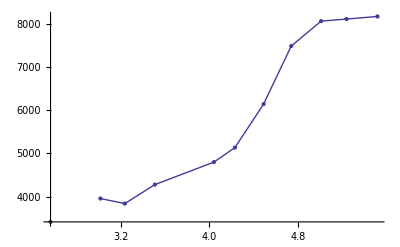

```mathematica
ListLinePlot[Transpose[{data[[All,1]],data[[All,3]]}],Mesh-> All]
```

Plot  estimated V_cc calculated from ADC1, y-axis vs. actual V_cc (x-axis)

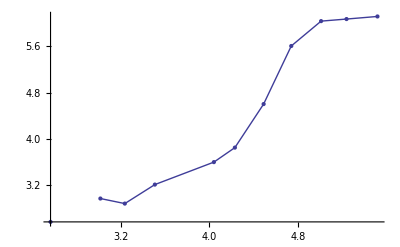

```mathematica
ListLinePlot[Transpose[{data[[All,1]],raw2volts[data[[All,3]]]*k/1000}],Mesh-> All]
```

Plot ADC0 raw value (measured temp, y-axis) vs. V_cc (x-axis). The tempearute around 20C during the experiment.

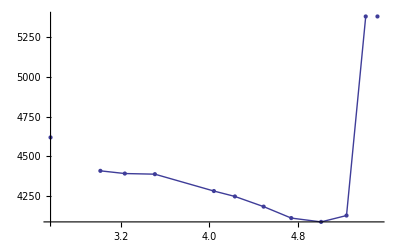

```mathematica
ListLinePlot[Transpose[{data[[All,1]],data[[All,2]]}],Mesh-> All]
```

Plot estimated temperature (y-axis) vs V_cc(x-axis)

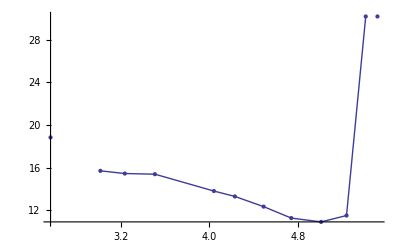

```mathematica
ListLinePlot[Transpose[{data[[All,1]],(raw2volts[data[[All,2]]] - 500)/10}],Mesh-> All]
```